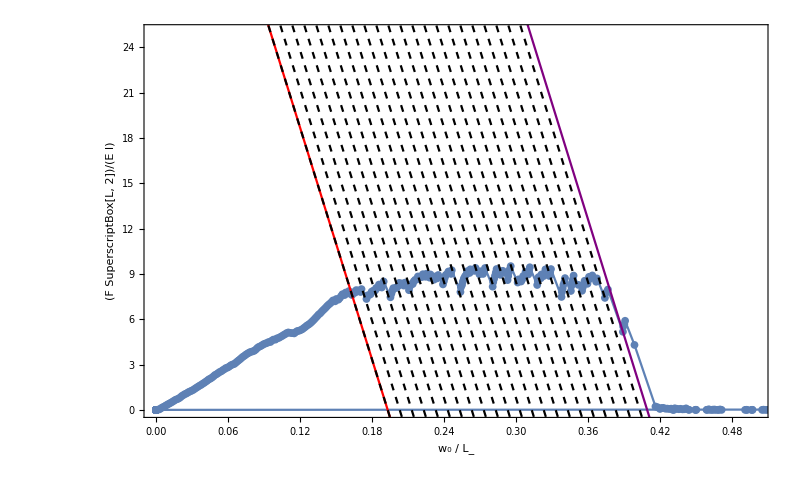

```mathematica
PSingleExp=Module[{n=14,P1,P2,P3},
P1 = ListPlot[fw0[[n]],PlotMarkers->{Automatic,8},PlotRange->{{0.0,0.5},{0,25}},ImageSize->800,GridLines->None,Ticks->Automatic,Joined->True,
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False];P2  = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]]},
Obline[x_,wsi_] = k (wsi - x);
(*NSolve[Obline[x,wss]==]*)
Plot[{Obline[x,wss],Obline[x,wsf]}, {x, 0, 0.5},PlotStyle->{Red,Purple}]
];
P3 = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]]},
Obline[x_,wsi_] = k (wsi - x);
 Plot[Obline[x,#]&/@Range[wss,wsf,0.01], {x, 0, 0.5},PlotStyle->{Dashed,Black}]
];
Show[P1,P2,P3]]
```

```mathematica
fw0[[14,;;,1]];
LeftIndex=Select[fw0[[14,;;,1]],0.04>#>0.0&]//Length;
RightIndex=Select[fw0[[14,;;,1]],0.375>#>0.0&]//Length;
data2=fw0[[14,LeftIndex;;RightIndex]];
```

```mathematica
basis=x^#&/@Range@10
```

{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}

```mathematica
SolutionVector01[[161,-1,1]]
```

0.78562

```mathematica
μ0p32=SolutionVector01[[161,;;1090,{1,2}]];
```

```mathematica
μ0p32f[x_]=Fit[μ0p32,{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x]
```

47.9992 x+55.3903 x^2-484.584 x^3-418.306 x^4+2009.99 x^5+12615.8 x^6-64495.1 x^7+121150. x^8-108418. x^9+38441.1 x^10

```mathematica
fdata2[x_]=Fit[data2,{x,x^2},x]
```

61.0333 x-104.15 x^2

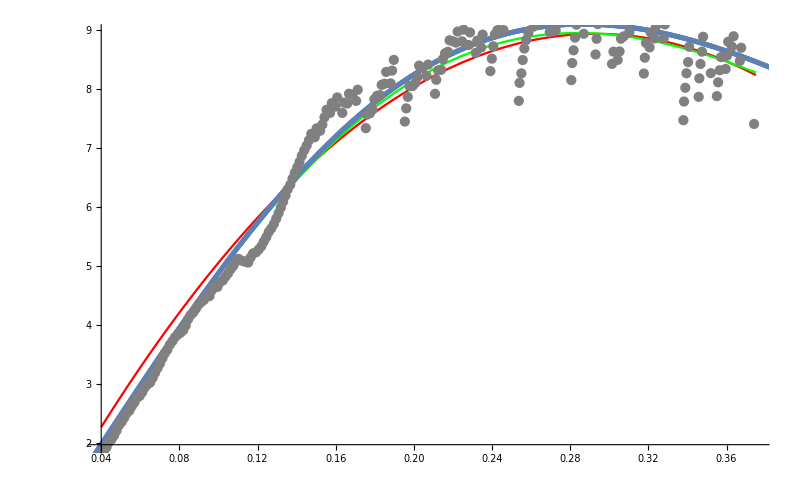

```mathematica
Show[Plot[{fdata2[x],μ0p32f[x]},{x,0.04,0.375},PlotStyle->{Red,Green}],ListPlot[SolutionVector01[[160,;;,{1,2}]]],ListPlot[data2,PlotStyle->Gray]]
```

## Inverse method to fit the exact data

```mathematica
data2=fw0[[14,LeftIndex;;RightIndex]];
```

```mathematica
data2//Dimensions
```

{230,2}

```mathematica
data3=Transpose@{data2[[;;,1]],data2[[;;,2]]-μ0p32f/@data2[[;;,1]]};
```

```mathematica
intf[x_]=Interpolation[data3,InterpolationOrder->1][x]
```

InterpolatingFunction[…][x]

```mathematica
wholef[x_]=Piecewise[{{0,x≤data3[[1,1]]},{intf[x],data3[[1,1]]<x<data3[[-1,1]]},{0,x≥data3[[-1,1]]}}]
```

Piecewise[{{0, x≤0.0375117}, {InterpolatingFunction[…][x], 0.0375117<x<0.374084}, {0, True}}]

```mathematica
?Amplitude
```

Global`Amplitude

Amplitude[x_]=26.35 x

```mathematica
Amplitude[x_]=(10 x/μ0p32[[-1,1]])
```

26.35 x

```mathematica
RealFriction[x_]=wholef[x]/Amplitude[x]
```

(0.0379507 (Piecewise[{{0, x≤0.0375117}, {InterpolatingFunction[…][x], 0.0375117<x<0.374084}, {0, True}}]))/x

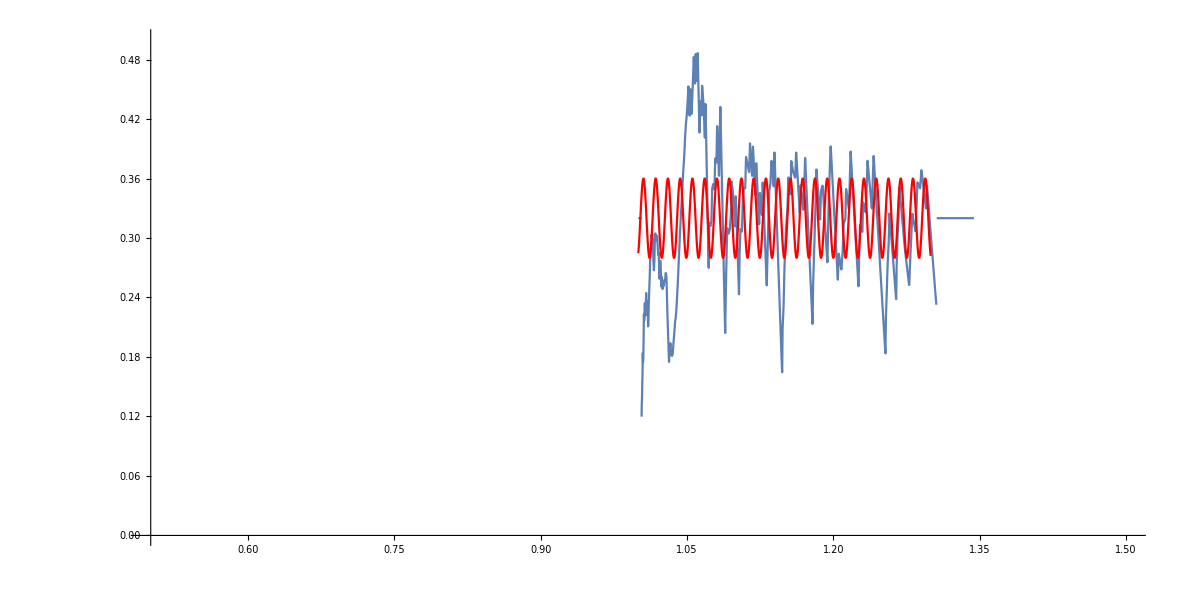

```mathematica
Show[ParametricPlot[{ArcOfw0[x],RealFriction[x]+0.32},{x,0,0.4},PlotRange->{{0.5,1.5},{0,0.5}}],
Plot[0.32+0.04 Cos[x/0.002],{x,1,1.3},PlotStyle->Red]]
```

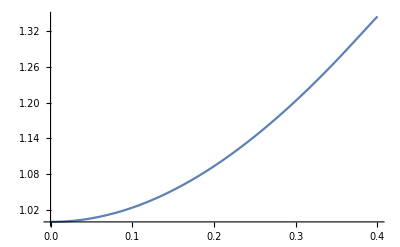

```mathematica
Plot[ArcOfw0[x],{x,0,0.4}]
```

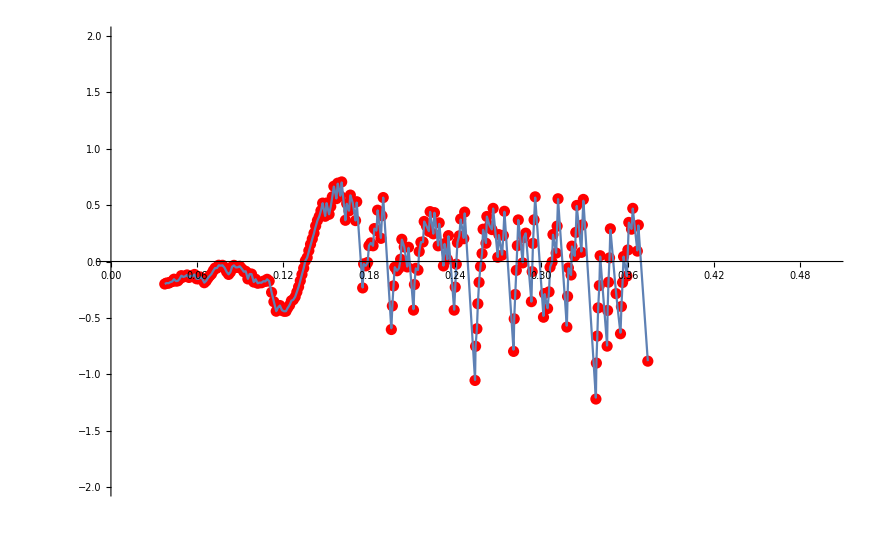

```mathematica
Plot[ArcOfw0[x],{x,0,0.4}];
Show[ListPlot[data3,PlotStyle->Red],Plot[Interpolation[data3,InterpolationOrder->1][x],{x,data3[[1,1]],data3[[-1,1]]}],PlotRange->{{0.0,0.5},{-2,2}}]
```

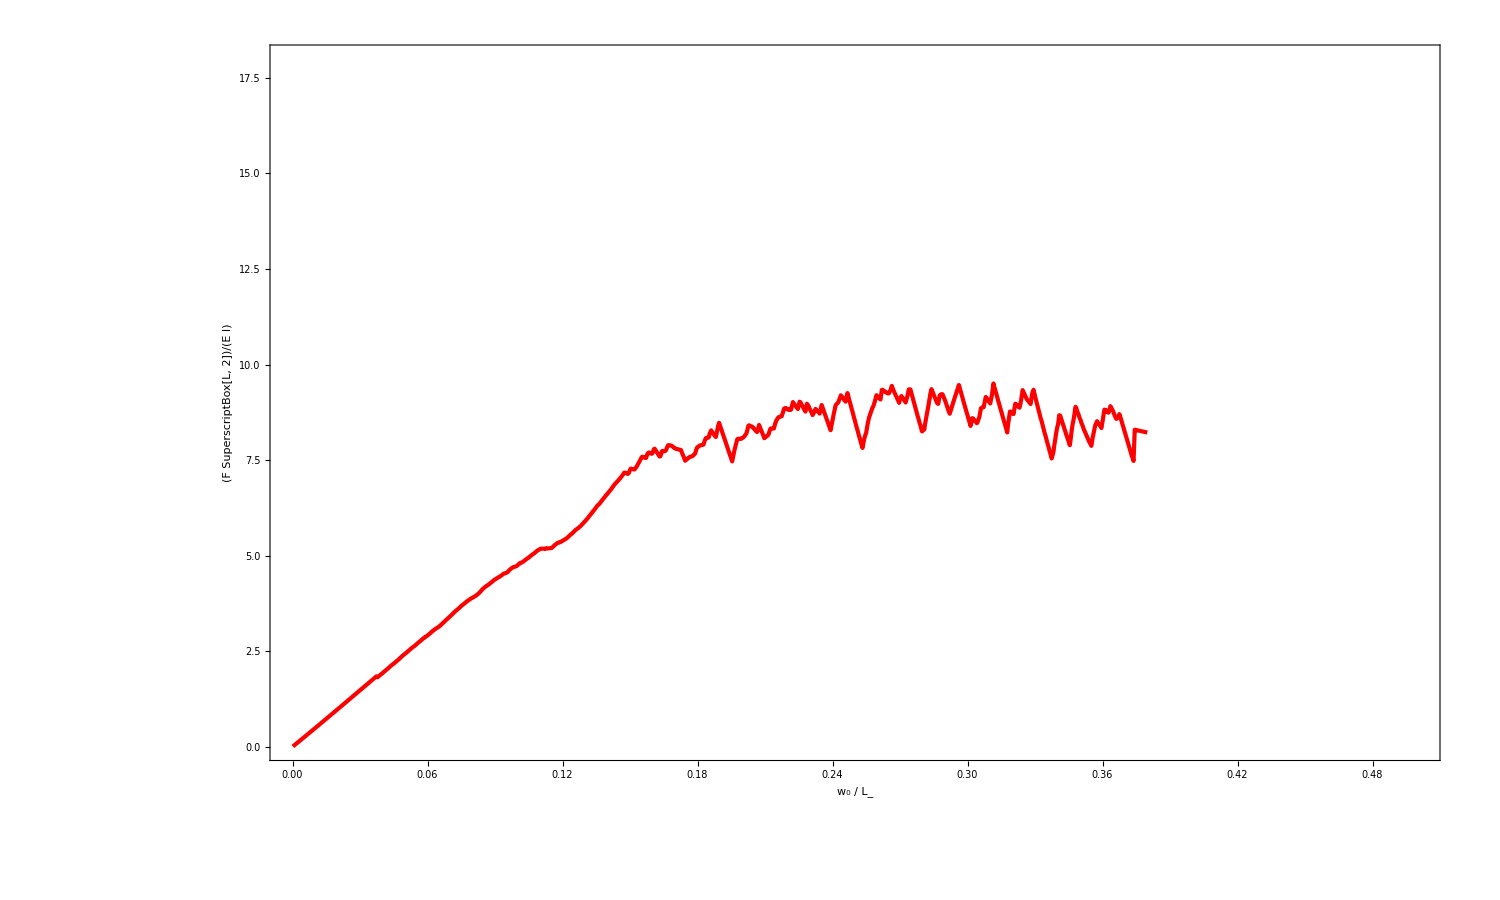

```mathematica
Psinutry=Module[{μ0={0.32},A = 0.04,λ=0.002},
deflect=SolutionVector01[[;;,;;,1]];
arclength=SolutionVector01[[;;,;;,5]];
frictionC=SolutionVector01[[;;,;;,6]];
levelset=frictionC-Map[Map[RealFriction],deflect];
data1=Flatten[Table[{SolutionVector01[[i,j,1]],SolutionVector01[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector01},{j,1,Length[SolutionVector01[[i]]]}],1];
	Level0p1=Table[Select[data1,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
Level0p1S=(SortBy[Level0p1[[#]],First])&/@Range@Length@μ0;
Level3=Level0p1S[[;;,;;,{1,2}]];
FailureIndex=Select[Level3[[1,;;,1]],#<0.38&]//Length;
ListPlot[Level3[[1,;;FailureIndex]],
Joined->True,
PlotStyle->Directive[Red,Thickness[0.002]],ImageSize->1500,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.5},{0,18}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]]
```

```mathematica
Map[Map[Amplitude],deflect][[1,1]]
```

0.00439166

### Systematic subroutine

#### For test N = 1

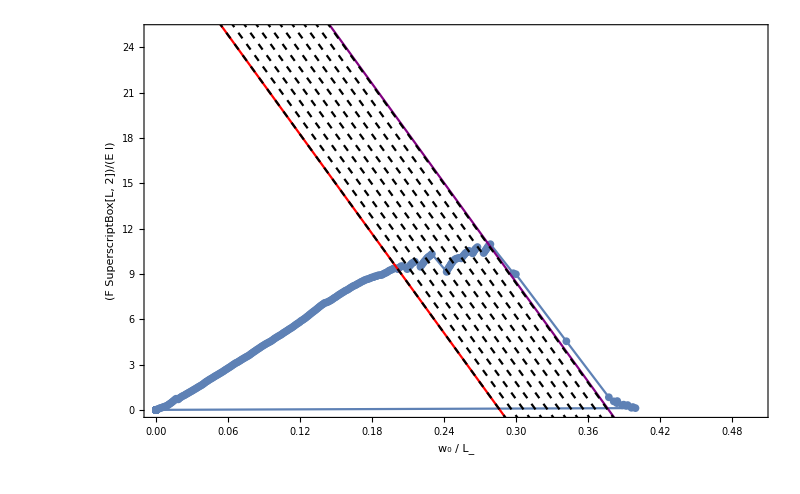

```mathematica
PSingleExp=Module[{n=25,P1,P2,P3},
P1 = ListPlot[fw0[[n]],PlotMarkers->{Automatic,8},PlotRange->{{0.0,0.5},{0,25}},ImageSize->800,GridLines->None,Ticks->Automatic,Joined->True,
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False];P2  = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]]},
Obline[x_,wsi_] = k (wsi - x);
(*NSolve[Obline[x,wss]==]*)
Plot[{Obline[x,wss],Obline[x,wsf]}, {x, 0, 0.5},PlotStyle->{Red,Purple}]
];
P3 = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]]},
Obline[x_,wsi_] = k (wsi - x);
 Plot[Obline[x,#]&/@Range[wss,wsf,0.01], {x, 0, 0.5},PlotStyle->{Dashed,Black}]
];
Show[P1,P2,P3]]
```

#### Choose a proper interval

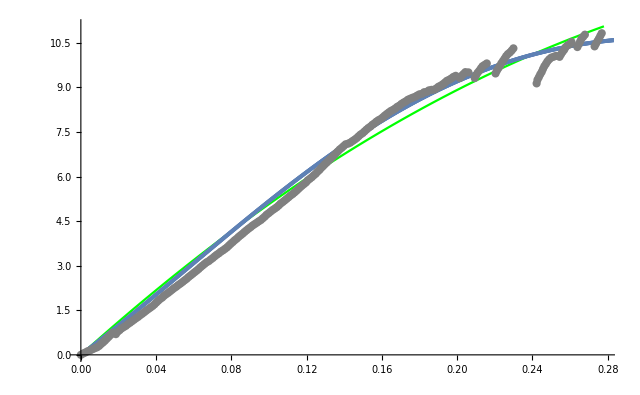

```mathematica
Module[{n=25,μN=256},
Startw0=0.0;
Endw0=0.278;
fw0[[n,;;,1]];
LeftIndex=Select[fw0[[n,;;,1]],Startw0>#>0.0&]//Length;
RightIndex=Select[fw0[[n,;;,1]],Endw0>#>0.0&]//Length;
data2=fw0[[n,1;;RightIndex]];
fdata2[x_]=Fit[data2,{x,x^2(*,x^3*)},x];
Show[Plot[fdata2[x],{x,0.0,Endw0},PlotStyle->{Red,Green}],ListPlot[SolutionVector01[[μN,;;,{1,2}]]],ListPlot[data2,PlotStyle->Gray]]]
```

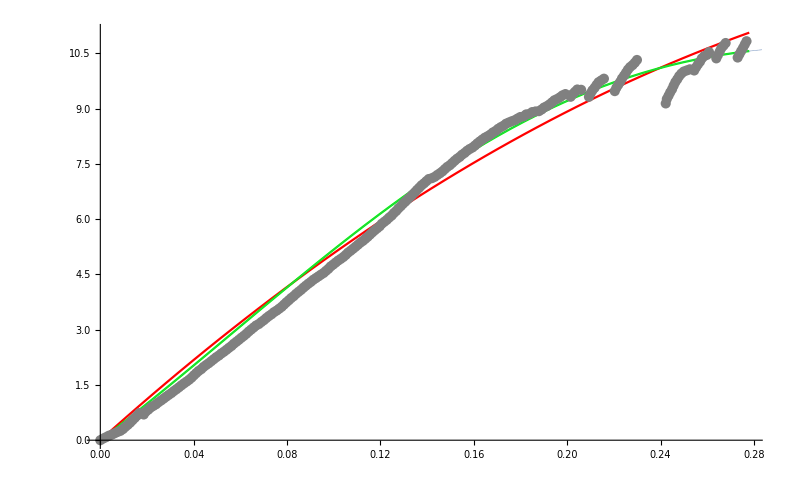

```mathematica
Module[{μN=256},
EndIndex=Select[SolutionVector01[[μN,;;,1]],#<Endw0&]//Length;
μAve=SolutionVector01[[μN,;;EndIndex,{1,2}]];
μAvef[x_]=Fit[μAve,{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
Show[Plot[{fdata2[x],μAvef[x]},{x,0.0,Endw0},PlotStyle->{Red,Green}],ListPlot[SolutionVector01[[μN,;;,{1,2}]],PlotMarkers->{Automatic,0.01}],ListPlot[data2,PlotStyle->Gray]]]
```

0.51

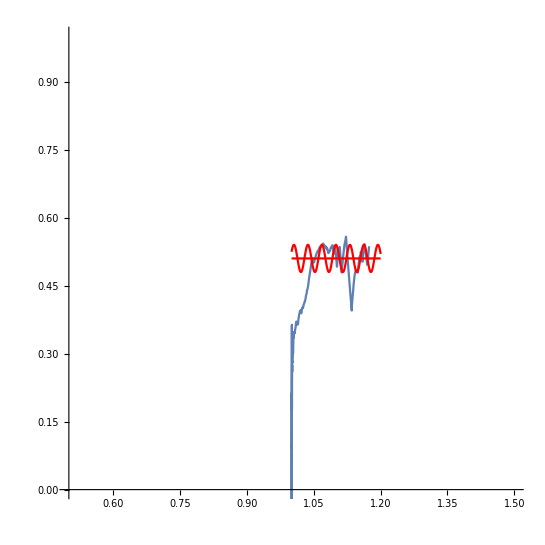

```mathematica
Module[{μN=256},
data3=Transpose@{data2[[;;,1]],data2[[;;,2]]-μAvef/@data2[[;;,1]]};
intf[x_]=Interpolation[data3,InterpolationOrder->1][x];
wholef[x_]=Piecewise[{{0,x≤data3[[1,1]]},{intf[x],data3[[1,1]]<x<data3[[-1,1]]},{0,x≥data3[[-1,1]]}}];
Amplitude[x_]=(10 x/μAve[[-1,1]]);
RealFriction[x_]=wholef[x]/Amplitude[x];
μ0=SolutionVector01[[μN,1,6]];
Print@μ0;
Arcofw =SolutionVector01[[μN,;;EndIndex,{1,5}]];
ArcOfw0[x]=Fit[Arcofw,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
Show[ParametricPlot[{ArcOfw0[x],RealFriction[x]+μ0},{x,0,Endw0},PlotRange->{{0.5,1.5},{0,1}}],
Plot[{μ0,μ0+0.03 Cos[x/0.005]},{x,1,1.2},PlotStyle->Red]]]
```

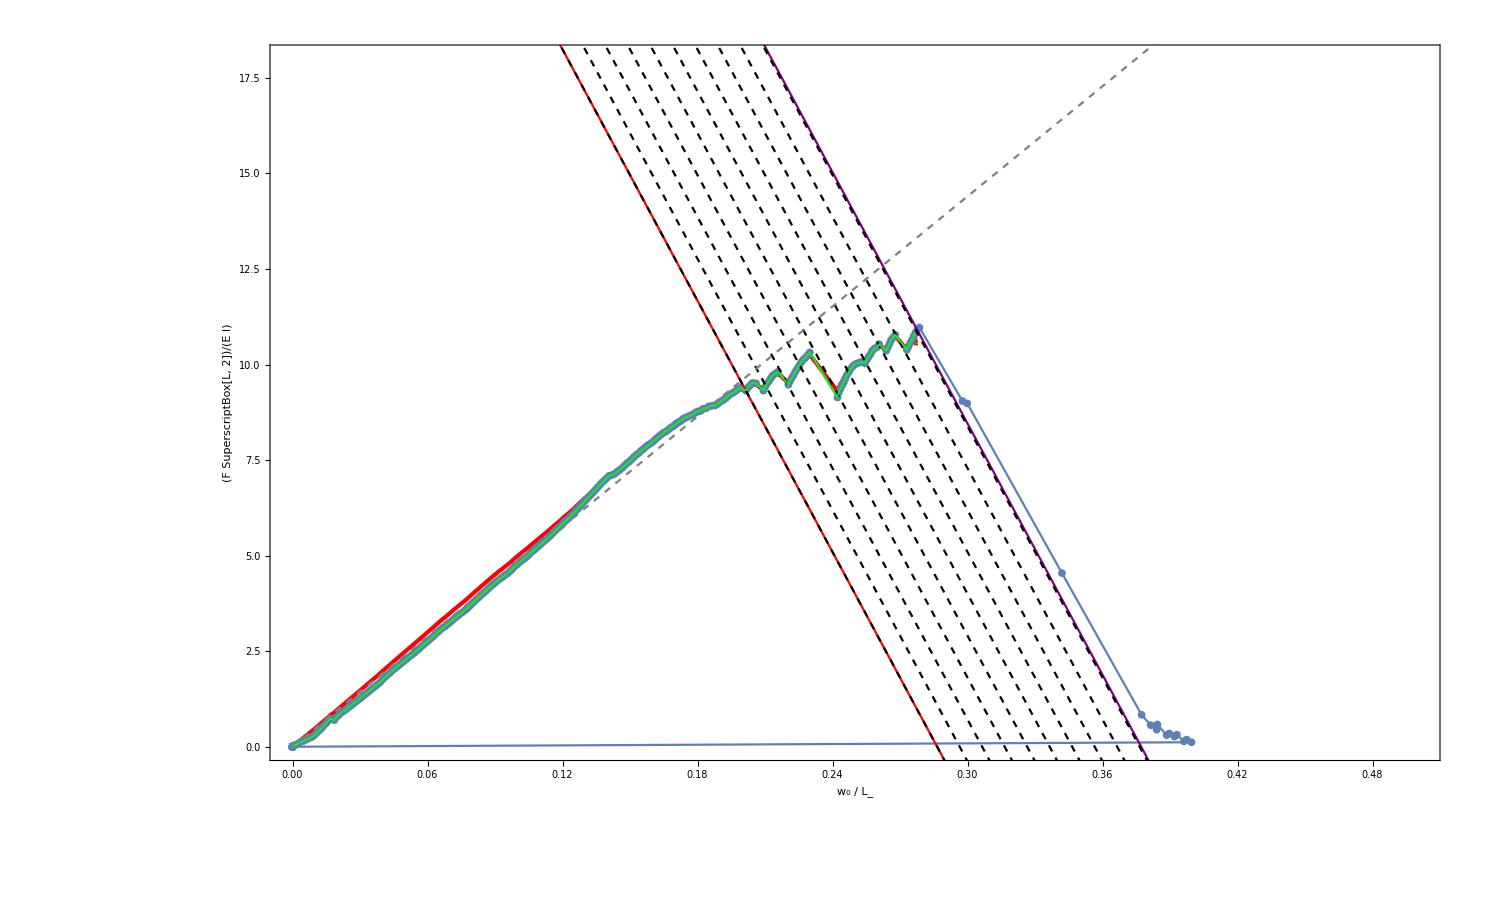

```mathematica
Psinutry=Module[{μ0={0.51}},
deflect=SolutionVector01[[;;,;;,1]];
arclength=SolutionVector01[[;;,;;,5]];
frictionC=SolutionVector01[[;;,;;,6]];
levelset=frictionC-Map[Map[RealFriction],deflect];
data1=Flatten[Table[{SolutionVector01[[i,j,1]],SolutionVector01[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector01},{j,1,Length[SolutionVector01[[i]]]}],1];
	Level0p1=Table[Select[data1,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
Level0p1S=(SortBy[Level0p1[[#]],First])&/@Range@Length@μ0;
Level3=Level0p1S[[;;,;;,{1,2}]];
FailureIndex=Select[Level3[[1,;;,1]],#<Endw0&]//Length;
ListPlot[Level3[[1,;;FailureIndex]],
Joined->True,
PlotStyle->Directive[Red,Thickness[0.002]],ImageSize->1500,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.5},{0,18}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]];
Psimu=Plot[μAvef[x]+wholef[x],{x,0,Endw0},PlotStyle->{Thickness[0.0008],Green}];
Show[Psinutry,PSingleExp,Psimu]
```

#### For test N = 8

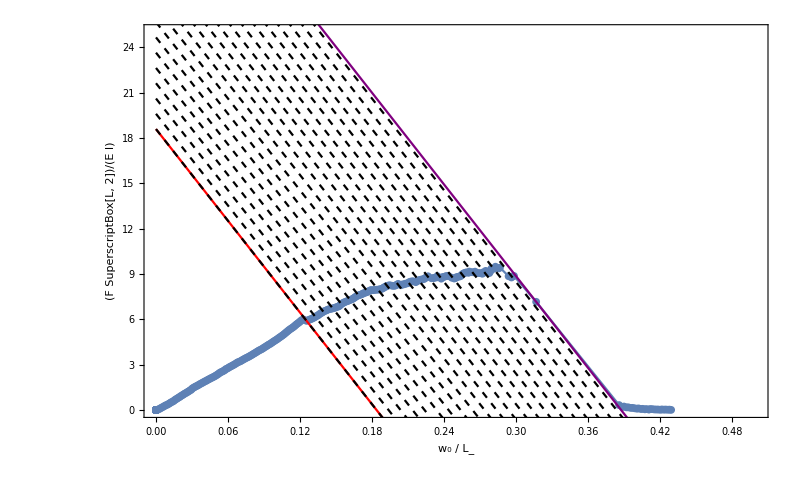

```mathematica
PSingleExp=Module[{n=8,P1,P2,P3},
P1 = ListPlot[fw0[[n]],PlotMarkers->{Automatic,8},PlotRange->{{0.0,0.5},{0,25}},ImageSize->800,GridLines->None,Ticks->Automatic,Joined->True,
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False];P2  = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]]},
Obline[x_,wsi_] = k (wsi - x);
(*NSolve[Obline[x,wss]==]*)
Plot[{Obline[x,wss],Obline[x,wsf]}, {x, 0, 0.5},PlotStyle->{Red,Purple}]
];
P3 = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]]},
Obline[x_,wsi_] = k (wsi - x);
 Plot[Obline[x,#]&/@Range[wss,wsf,0.01], {x, 0, 0.5},PlotStyle->{Dashed,Black}]
];
Show[P1,P2,P3]]
```

#### Choose a proper interval

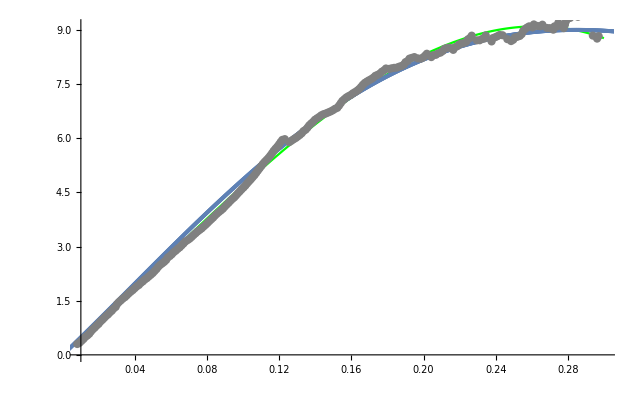

```mathematica
Module[{n=8,μN=164},
Startw0=0.01;
Endw0=0.3;
fw0[[n,;;,1]];
LeftIndex=Select[fw0[[n,;;,1]],Startw0>#>0.0&]//Length;
RightIndex=Select[fw0[[n,;;,1]],Endw0>#>0.0&]//Length;
data2=fw0[[n,LeftIndex;;RightIndex]];
fdata2[x_]=Fit[data2,{x,x^2,x^3},x];
Show[Plot[fdata2[x],{x,Startw0,Endw0},PlotStyle->{Red,Green}],ListPlot[SolutionVector01[[μN,;;,{1,2}]]],ListPlot[data2,PlotStyle->Gray]]]
```

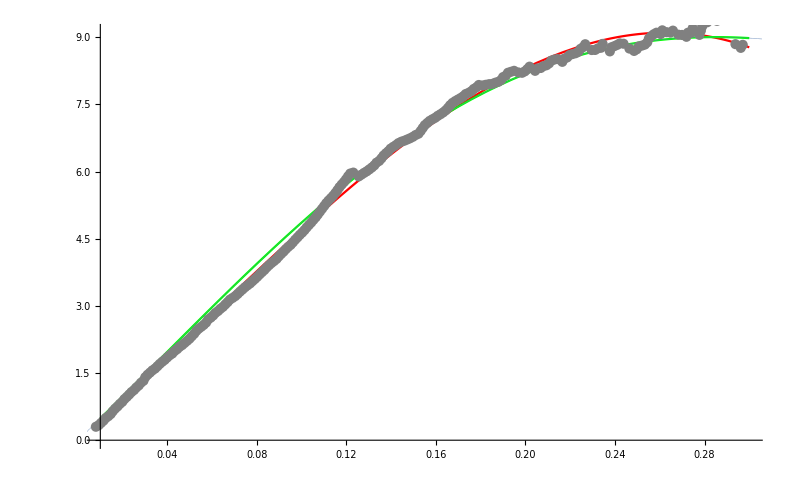

```mathematica
Module[{μN=164},
EndIndex=Select[SolutionVector01[[μN,;;,1]],#<Endw0&]//Length;
μAve=SolutionVector01[[μN,;;EndIndex,{1,2}]];
μAvef[x_]=Fit[μAve,{x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
Show[Plot[{fdata2[x],μAvef[x]},{x,Startw0,Endw0},PlotStyle->{Red,Green}],ListPlot[SolutionVector01[[μN,;;,{1,2}]],PlotMarkers->{Automatic,0.01}],ListPlot[data2,PlotStyle->Gray]]]
```

0.326

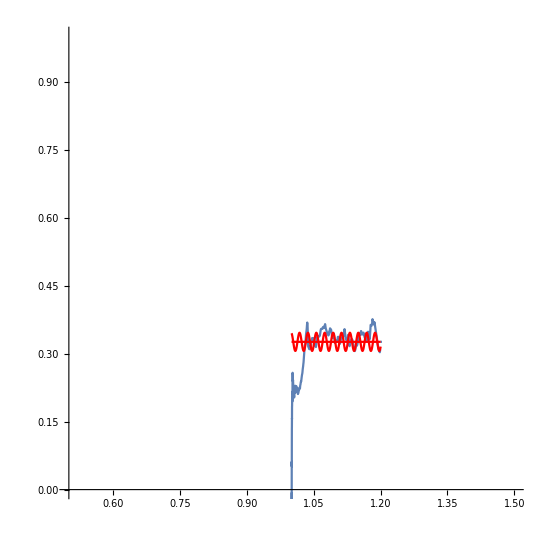

```mathematica
Module[{μN=164},
data3=Transpose@{data2[[;;,1]],data2[[;;,2]]-μAvef/@data2[[;;,1]]};
intf[x_]=Interpolation[data3,InterpolationOrder->1][x];
wholef[x_]=Piecewise[{{0,x≤data3[[1,1]]},{intf[x],data3[[1,1]]<x<data3[[-1,1]]},{0,x≥data3[[-1,1]]}}];
Amplitude[x_]=(10 x/μAve[[-1,1]]);
RealFriction[x_]=wholef[x]/Amplitude[x];
μ0=SolutionVector01[[μN,1,6]];
Print@μ0;
Arcofw =SolutionVector01[[μN,;;EndIndex,{1,5}]];
ArcOfw0[x]=Fit[Arcofw,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
Show[ParametricPlot[{ArcOfw0[x],RealFriction[x]+μ0},{x,0,Endw0},PlotRange->{{0.5,1.5},{0,1}}],
Plot[{μ0,μ0+0.02 Cos[x/0.003]},{x,1,1.2},PlotStyle->Red]]]
```

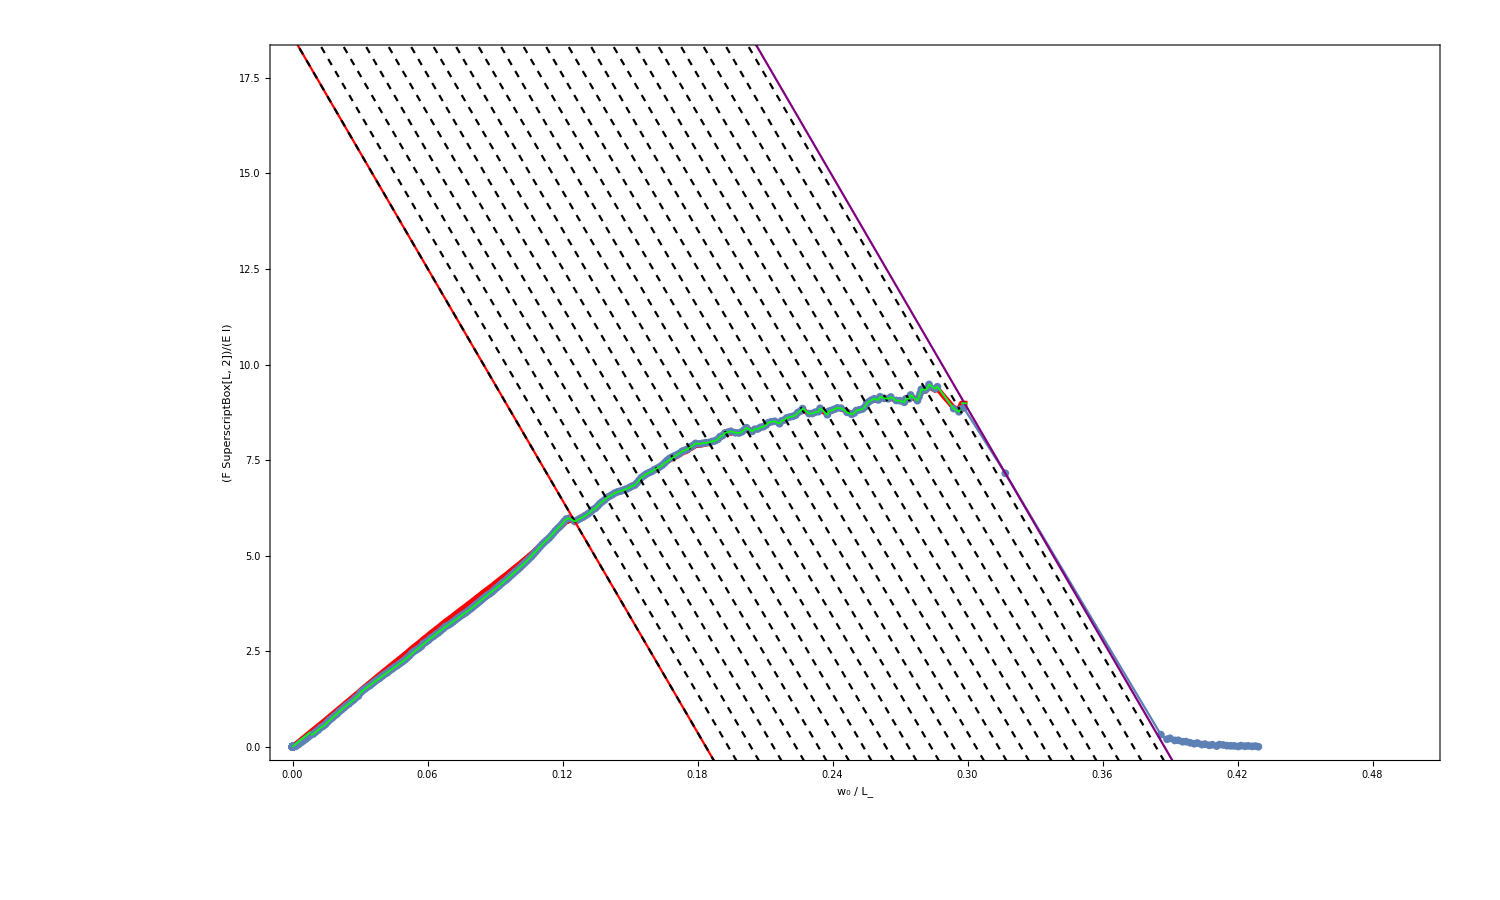

```mathematica
Psinutry=Module[{μ0={0.326}},
deflect=SolutionVector01[[;;,;;,1]];
arclength=SolutionVector01[[;;,;;,5]];
frictionC=SolutionVector01[[;;,;;,6]];
levelset=frictionC-Map[Map[RealFriction],deflect];
data1=Flatten[Table[{SolutionVector01[[i,j,1]],SolutionVector01[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector01},{j,1,Length[SolutionVector01[[i]]]}],1];
	Level0p1=Table[Select[data1,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
Level0p1S=(SortBy[Level0p1[[#]],First])&/@Range@Length@μ0;
Level3=Level0p1S[[;;,;;,{1,2}]];
FailureIndex=Select[Level3[[1,;;,1]],#<Endw0&]//Length;
ListPlot[Level3[[1,;;FailureIndex]],
Joined->True,
PlotStyle->Directive[Red,Thickness[0.0025]],ImageSize->1500,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.5},{0,18}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]];
Psimu=Plot[μAvef[x]+wholef[x],{x,0,Endw0},PlotStyle->{Thickness[0.0008],Green}];
Show[Psinutry,PSingleExp,Psimu]
```